# n(n-1,.....)=Prime

ضرب العدد  في عدد اصغر منه هل سيكون هناك دائمما عدد اولي

```mathematica
Table[Boole@PrimeQ[n*Range[n-1]+1],{n,2,20}]//Column
```

{1}
{0,1}
{1,0,1}
{0,1,0,0}
{1,1,1,0,1}
{0,0,0,1,0,1}
{0,1,0,0,1,0,0}
{0,1,0,1,0,0,0,1}
{1,0,1,1,0,1,1,0,0}
{0,1,0,0,0,1,0,1,0,0}
{1,0,1,0,1,1,0,1,1,0,0}
{0,0,0,1,0,1,0,0,0,1,0,1}
{0,1,1,0,1,0,0,1,1,0,0,0,0}
{0,1,0,1,0,0,0,0,0,1,0,1,0,1}
{1,0,0,0,0,1,1,0,0,0,0,1,0,0,1}
{0,0,0,0,0,1,0,1,0,0,0,0,0,1,0,0}
{1,1,0,1,0,1,1,0,1,1,1,0,0,0,1,0,1}
{0,0,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0}
{0,1,1,0,1,0,0,0,1,0,0,1,0,1,0,0,0,0,0}

```mathematica
Length/@((Table[Boole@PrimeQ[n*Range[n-1]+1]//Last,{n,2,5000}]//Split)/.{0..}->Sequence[])
```

{3,2,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,1,2,1,1,1,2,1,2,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,2,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1}

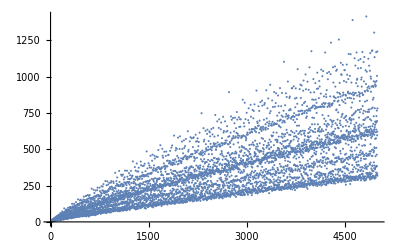

```mathematica
Table[Boole@PrimeQ[n*Range[n-1]+1]//Total,{n,2,5000}]//ListPlot
```

```mathematica
Table[Boole@PrimeQ[Prime[n]*Range[n-1]+1],{n,2,50}]//ArrayPlot
```

-Graphics-